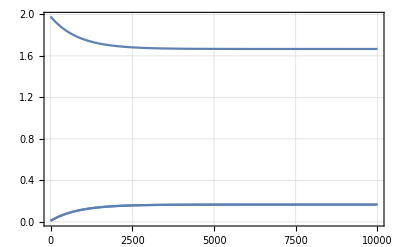

{{1.66667,0.166666,0.166666}}

```mathematica
(* numberOfAminoAcids = 1 *)

d0[x_?VectorQ]:=
Total[
{ 
0.001*x[[3]],
-0.0001*x[[1]],
0.001*x[[2]],
-0.0001*x[[1]]
}
];

d1[x_?VectorQ]:=
Total[
{ 
-0.001*x[[2]],
0.0001*x[[1]]
}
];

d2[x_?VectorQ]:=
Total[
{ 
-0.001*x[[3]],
0.0001*x[[1]]
}
];

d[x_?VectorQ]:={d0[x],d1[x],d2[x]};

v = 0.01;
ee = 0.01;
tMax = 10000;

x0={2*(1-v),v*(1+ee), v* (1-ee)};
sol =NDSolve[{D[x[t],t]==d[x[t]], x[0]==x0},x,{t, 0, tMax}];
Plot[x[t]/. sol, {t, 0, tMax}, Frame->True, GridLines->Automatic]

x[t] /. sol /. {t -> tMax}
```

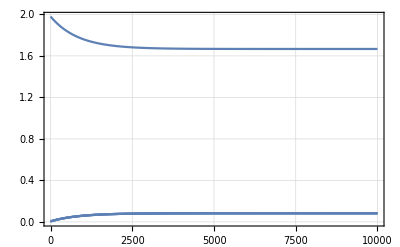

{{1.66667,0.0833329,0.0833328,0.0833329,0.0833328}}

```mathematica
(* numberOfAminoAcids = 2 *)

d0[x_?VectorQ]:=
Total[
{ 
0.001*x[[5]],
-0.0001*x[[1]]/2,
0.001*x[[3]],
-0.0001*x[[1]]/2,
0.001*x[[4]],
-0.0001*x[[1]]/2,
0.001*x[[2]],
-0.0001*x[[1]]/2
}
];

d1[x_?VectorQ]:=
Total[
{ 
-0.001*x[[2]],
0.0001*x[[1]]/2
}
];

d2[x_?VectorQ]:=
Total[
{ 
-0.001*x[[3]],
0.0001*x[[1]]/2
}
];

d3[x_?VectorQ]:=
Total[
{ 
-0.001*x[[4]],
0.0001*x[[1]]/2
}
];

d4[x_?VectorQ]:=
Total[
{ 
-0.001*x[[5]],
0.0001*x[[1]]/2
}
];


d[x_?VectorQ]:={d0[x],d1[x],d2[x],d3[x],d4[x]};

v = 0.01;
ee = 0.01;
tMax = 10000;

x0={2*(1-v),v*(1+ee)/2, v* (1-ee)/2,v*(1+ee)/2, v* (1-ee)/2};

sol =NDSolve[{D[x[t],t]==d[x[t]], x[0]==x0},x,{t, 0, tMax}];
Plot[x[t]/. sol, {t, 0, tMax}, Frame->True, GridLines->Automatic]

x[t] /. sol /. {t -> tMax}
```